```mathematica
(*1 CFM = 0.00047194745 m^3/s*)
(*1 Subscript[mmH, 2] O=9.80665 Pa*)
```

59867.7

76543.9

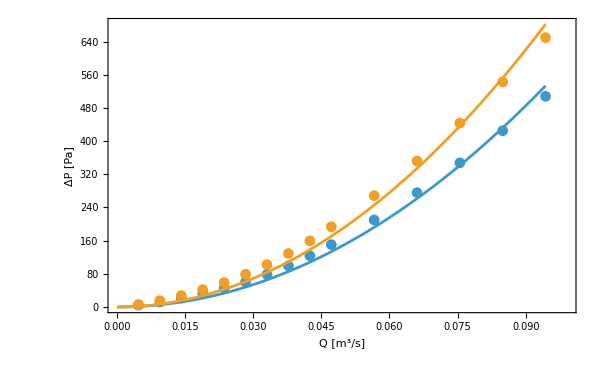

```mathematica
(*R2.1*)t={{10,4.484,5.86},{20,12.08,15.46},{30,21.4,27.55},{40,32.33,41.91},{50,45.26,58.91},{60,60.57,78.92},{70,78.48,102.1},{80,99.41,128.9},{90,123.5,159.5},{100,150.4,193.4},{120,209.8,268.4},{140,275.8,352},{160,347.5,443.4},{180,424.9,542.6},{200,507.9,649.4}};
t=Table[{0.00047194745t[[i,1]],t[[i,2]],t[[i,3]]},{i,1,Length[t]}];
a1=a/.FindFit[t[[All,{1,2}]],a x^2,a,x]
a2=a/.FindFit[t[[All,{1,3}]],a x^2,a,x]
Show[ListPlot[{t[[All,{1,2}]],t[[All,{1,3}]]},PlotRange->{{0,1.05t[[-1,1]]},{0,1.05t[[-1,3]]}},Joined->False,Mesh->All,Frame->True,ImageSize->600,FrameStyle->Directive[Black,18],FrameLabel->{"Q [m^3/s]","ΔP [Pa]"}],Plot[{a1 x^2,a2 x^2},{x,0,t[[-1,1]]}]]
```

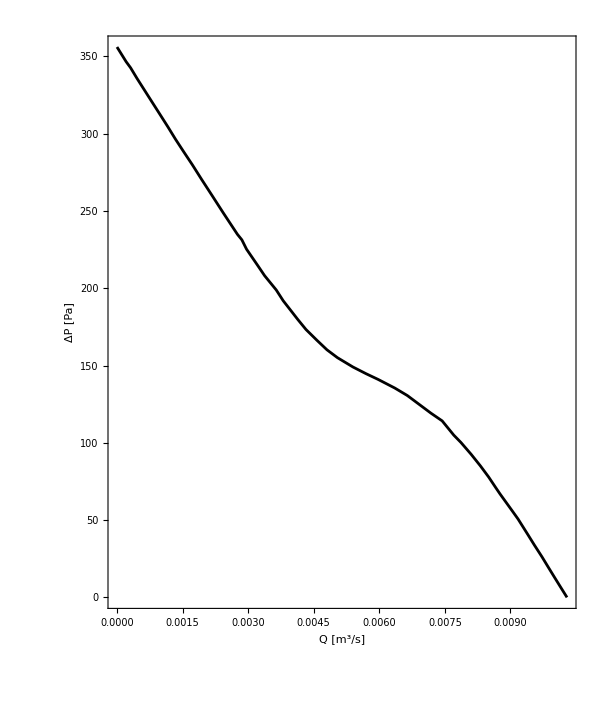

```mathematica
SetDirectory[NotebookDirectory[]];
(*Data_sheet_PFB0412EHN-TP06.pdf, mmH20 vs CFM*)
data=Sort[Import["../data/PQ.dat"]];
data=Table[{0.00047194745data[[i,1]], 9.8066data[[i,2]]},{i,1,Length[data]}];
ListPlot[data,PlotStyle->Black,AspectRatio->1.2,Frame->True,FrameLabel->{"Q [m^3/s]","ΔP [Pa]"},ImageSize->600,FrameStyle->Directive[Black,18],PlotRange->{{0,data[[-1,1]]},Automatic},Joined->True]
Vref=12.;
Powref=6.;
ShiftData[nfans_,list_,V_,Vref_]:=Table[{nfans list[[i,1]] V/Vref,list[[i,2]](V/Vref)^2},{i,1,Length[list]}]
ShiftDataEff[nfans_,list_,V_,Vref_]:=Table[{nfans list[[i,1]] V/Vref,1/Powref list[[i,2]]list[[i,1]]},{i,1,Length[list]}]
fshift[nfans_,list_,V_,Vref_,Q_]:=Interpolation[ShiftData[nfans,list,V,Vref]][Q]
fshifteff[nfans_,list_,V_,Vref_,Q_]:=Interpolation[ShiftDataEff[nfans,list,V,Vref]][Q]
```

```mathematica
Z=(a1+a2)/2;
factor=2000;
Vmin=10.8;
Vmax=13.2;
Manipulate[Plot[{fshift[nfans,data,V,Vref,Q],factor fshifteff[nfans,data,V,Vref,Q],Z Q^2},{Q,0,10 nfans data[[-1,1]] V/Vref},PlotRange->{{0,nfans 1.01data[[-1,1]] Vmax/Vref},{0, 1.1data[[1,2]](Vmax/Vref)^2}},AspectRatio->1.2,Frame->True,FrameLabel->{"Q [m^3/s]","P [Pa]"},FrameStyle->Directive[Black,18],ImageSize->600,PlotStyle->{Black,{Red,Dashed},{Blue,DotDashed}},Epilog->{Inset[StringJoin["V = ",ToString[V]],Scaled[{0.9,0.9}]],Dashed,Line[{{Q/.FindRoot[Z Q^2==fshift[nfans,data,V,Vref,Q],{Q,data[[-1,1]] V/Vref}],0},{Q/.FindRoot[Z Q^2==fshift[nfans,data,V,Vref,Q],{Q,data[[-1,1]] V/Vref}],10^3}}]},FrameTicks->{{Automatic,Table[{factor i,If[Mod[100 i,5]==0,i,None]},{i,0,1,0.005}]},{Automatic,Automatic}}],{{V,Vref},10.8,13.2},{nfans,1,10,1}]
```

```mathematica
fV[nfans_,data_,V_,Vref_]:={Q/.FindRoot[Z Q^2==fshift[nfans,data,V,Vref,Q],{Q,data[[-1,1]] V/Vref}],Z(Q/.FindRoot[Z Q^2==fshift[nfans,data,V,Vref,Q],{Q,data[[-1,1]] V/Vref}])^2,Z(Q/.FindRoot[Z Q^2==fshift[nfans,data,V,Vref,Q],{Q,data[[-1,1]] V/Vref}])^3,fshifteff[nfans,data,V,Vref,Q/.FindRoot[Z Q^2==fshift[nfans,data,V,Vref,Q],{Q,data[[-1,1]] V/Vref}]],(Z(Q/.FindRoot[Z Q^2==fshift[nfans,data,V,Vref,Q],{Q,data[[-1,1]] V/Vref}])^3)/(nfans(V/Vref)^3 Powref),(V/Vref)^3 Powref}
```

{{19.3336,4.374},{19.3515,4.38616},{19.3694,4.39835},{19.3873,4.41055},{19.4052,4.42278},{19.4231,4.43503},{19.441,4.44731},{19.459,4.4596},{19.4769,4.47192},{19.4948,4.48426},{19.5127,4.49663},{19.5306,4.50902},{19.5485,4.52143},{19.5664,4.53386},{19.5843,4.54631},{19.6022,4.55879},{19.6201,4.57129},{19.638,4.58382},{19.6559,4.59637},{19.6738,4.60894},{19.6917,4.62153},{19.7096,4.63414},{19.7275,4.64678},{19.7454,4.65944},{19.7633,4.67213},{19.7812,4.68484},{19.7991,4.69757},{19.817,4.71032},{19.8349,4.7231},{19.8528,4.7359},{19.8707,4.74872},{19.8886,4.76156},{19.9065,4.77443},{19.9244,4.78733},{19.9423,4.80024},{19.9602,4.81318},{19.9781,4.82614},{19.996,4.83913},{20.0139,4.85214},{20.0318,4.86517},{20.0497,4.87822},{20.0676,4.8913},{20.0855,4.9044},{20.1034,4.91753},{20.1213,4.93068},{20.1392,4.94385},{20.1571,4.95704},{20.175,4.97026},{20.1929,4.9835},{20.2108,4.99677},{20.2287,5.01006},{20.2466,5.02337},{20.2645,5.03671},{20.2824,5.05007},{20.3003,5.06345},{20.3182,5.07686},{20.3361,5.09029},{20.354,5.10374},{20.3719,5.11722},{20.3898,5.13072},{20.4077,5.14425},{20.4256,5.1578},{20.4435,5.17137},{20.4614,5.18497},{20.4793,5.19859},{20.4972,5.21223},{20.5151,5.2259},{20.533,5.2396},{20.5509,5.25331},{20.5688,5.26705},{20.5867,5.28082},{20.6046,5.2946},{20.6225,5.30842},{20.6405,5.32225},{20.6584,5.33611},{20.6763,5.35},{20.6942,5.3639},{20.7121,5.37784},{20.73,5.39179},{20.7479,5.40577},{20.7658,5.41978},{20.7837,5.43381},{20.8016,5.44786},{20.8195,5.46194},{20.8374,5.47604},{20.8553,5.49016},{20.8732,5.50431},{20.8911,5.51849},{20.909,5.53269},{20.9269,5.54691},{20.9448,5.56116},{20.9627,5.57543},{20.9806,5.58972},{20.9985,5.60404},{21.0164,5.61839},{21.0343,5.63276},{21.0522,5.64715},{21.0701,5.66157},{21.088,5.67601},{21.1059,5.69048},{21.1238,5.70497},{21.1417,5.71949},{21.1596,5.73403},{21.1775,5.7486},{21.1954,5.76319},{21.2133,5.7778},{21.2312,5.79244},{21.2491,5.8071},{21.267,5.82179},{21.2849,5.83651},{21.3028,5.85125},{21.3207,5.86601},{21.3386,5.8808},{21.3565,5.89561},{21.3744,5.91045},{21.3923,5.92531},{21.4102,5.9402},{21.4281,5.95511},{21.446,5.97005},{21.4639,5.98501},{21.4818,6.},{21.4997,6.01501},{21.5176,6.03005},{21.5355,6.04511},{21.5534,6.0602},{21.5713,6.07531},{21.5892,6.09045},{21.6071,6.10561},{21.625,6.1208},{21.6429,6.13602},{21.6608,6.15125},{21.6787,6.16652},{21.6966,6.18181},{21.7145,6.19712},{21.7324,6.21246},{21.7503,6.22782},{21.7682,6.24321},{21.7861,6.25863},{21.804,6.27407},{21.822,6.28954},{21.8399,6.30503},{21.8578,6.32054},{21.8757,6.33609},{21.8936,6.35165},{21.9115,6.36725},{21.9294,6.38287},{21.9473,6.39851},{21.9652,6.41418},{21.9831,6.42988},{22.001,6.4456},{22.0189,6.46134},{22.0368,6.47712},{22.0547,6.49291},{22.0726,6.50874},{22.0905,6.52459},{22.1084,6.54046},{22.1263,6.55636},{22.1442,6.57229},{22.1621,6.58824},{22.18,6.60422},{22.1979,6.62022},{22.2158,6.63625},{22.2337,6.65231},{22.2516,6.66839},{22.2695,6.6845},{22.2874,6.70063},{22.3053,6.71679},{22.3232,6.73297},{22.3411,6.74918},{22.359,6.76542},{22.3769,6.78168},{22.3948,6.79797},{22.4127,6.81429},{22.4306,6.83063},{22.4485,6.847},{22.4664,6.86339},{22.4843,6.87981},{22.5022,6.89626},{22.5201,6.91273},{22.538,6.92923},{22.5559,6.94575},{22.5738,6.9623},{22.5917,6.97888},{22.6096,6.99548},{22.6275,7.01211},{22.6454,7.02877},{22.6633,7.04545},{22.6812,7.06216},{22.6991,7.07889},{22.717,7.09565},{22.7349,7.11244},{22.7528,7.12926},{22.7707,7.1461},{22.7886,7.16296},{22.8065,7.17986},{22.8244,7.19678},{22.8423,7.21372},{22.8602,7.2307},{22.8781,7.2477},{22.896,7.26472},{22.9139,7.28178},{22.9318,7.29886},{22.9497,7.31596},{22.9676,7.3331},{22.9856,7.35026},{23.0035,7.36744},{23.0214,7.38466},{23.0393,7.4019},{23.0572,7.41917},{23.0751,7.43646},{23.093,7.45378},{23.1109,7.47113},{23.1288,7.4885},{23.1467,7.50591},{23.1646,7.52333},{23.1825,7.54079},{23.2004,7.55827},{23.2183,7.57578},{23.2362,7.59332},{23.2541,7.61088},{23.272,7.62847},{23.2899,7.64609},{23.3078,7.66373},{23.3257,7.68141},{23.3436,7.69911},{23.3615,7.71683},{23.3794,7.73459},{23.3973,7.75237},{23.4152,7.77017},{23.4331,7.78801},{23.451,7.80587},{23.4689,7.82376},{23.4868,7.84168},{23.5047,7.85962},{23.5226,7.87759},{23.5405,7.89559},{23.5584,7.91362},{23.5763,7.93167},{23.5942,7.94975},{23.6121,7.96786},{23.63,7.986}}

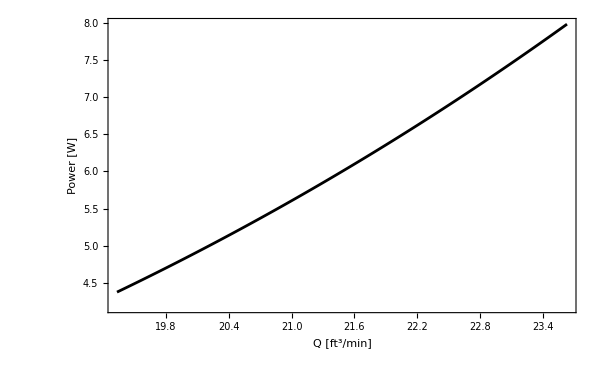

```mathematica
tV=Table[Join[{V},fV[1,data,V,Vref]],{V,10.8,13.2,0.01}];
tV1=Table[{tV[[i,2]]/0.00047194745,tV[[i,-1]]},{i,1,Length[tV]}]
ListPlot[tV1,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"Q [ft^3/min]","Power [W]"},ImageSize->600,AspectRatio->1/GoldenRatio,PlotRange->{{tV[[1,2]]/0.00047194745,tV[[-1,2]]/0.00047194745},All},FrameStyle->Directive[18,Black]]
```

```mathematica
tV1
```

{{19.3336,4.374},{19.3515,4.38616},{19.3694,4.39835},{19.3873,4.41055},{19.4052,4.42278},{19.4231,4.43503},{19.441,4.44731},{19.459,4.4596},{19.4769,4.47192},{19.4948,4.48426},{19.5127,4.49663},{19.5306,4.50902},{19.5485,4.52143},{19.5664,4.53386},{19.5843,4.54631},{19.6022,4.55879},{19.6201,4.57129},{19.638,4.58382},{19.6559,4.59637},{19.6738,4.60894},{19.6917,4.62153},{19.7096,4.63414},{19.7275,4.64678},{19.7454,4.65944},{19.7633,4.67213},{19.7812,4.68484},{19.7991,4.69757},{19.817,4.71032},{19.8349,4.7231},{19.8528,4.7359},{19.8707,4.74872},{19.8886,4.76156},{19.9065,4.77443},{19.9244,4.78733},{19.9423,4.80024},{19.9602,4.81318},{19.9781,4.82614},{19.996,4.83913},{20.0139,4.85214},{20.0318,4.86517},{20.0497,4.87822},{20.0676,4.8913},{20.0855,4.9044},{20.1034,4.91753},{20.1213,4.93068},{20.1392,4.94385},{20.1571,4.95704},{20.175,4.97026},{20.1929,4.9835},{20.2108,4.99677},{20.2287,5.01006},{20.2466,5.02337},{20.2645,5.03671},{20.2824,5.05007},{20.3003,5.06345},{20.3182,5.07686},{20.3361,5.09029},{20.354,5.10374},{20.3719,5.11722},{20.3898,5.13072},{20.4077,5.14425},{20.4256,5.1578},{20.4435,5.17137},{20.4614,5.18497},{20.4793,5.19859},{20.4972,5.21223},{20.5151,5.2259},{20.533,5.2396},{20.5509,5.25331},{20.5688,5.26705},{20.5867,5.28082},{20.6046,5.2946},{20.6225,5.30842},{20.6405,5.32225},{20.6584,5.33611},{20.6763,5.35},{20.6942,5.3639},{20.7121,5.37784},{20.73,5.39179},{20.7479,5.40577},{20.7658,5.41978},{20.7837,5.43381},{20.8016,5.44786},{20.8195,5.46194},{20.8374,5.47604},{20.8553,5.49016},{20.8732,5.50431},{20.8911,5.51849},{20.909,5.53269},{20.9269,5.54691},{20.9448,5.56116},{20.9627,5.57543},{20.9806,5.58972},{20.9985,5.60404},{21.0164,5.61839},{21.0343,5.63276},{21.0522,5.64715},{21.0701,5.66157},{21.088,5.67601},{21.1059,5.69048},{21.1238,5.70497},{21.1417,5.71949},{21.1596,5.73403},{21.1775,5.7486},{21.1954,5.76319},{21.2133,5.7778},{21.2312,5.79244},{21.2491,5.8071},{21.267,5.82179},{21.2849,5.83651},{21.3028,5.85125},{21.3207,5.86601},{21.3386,5.8808},{21.3565,5.89561},{21.3744,5.91045},{21.3923,5.92531},{21.4102,5.9402},{21.4281,5.95511},{21.446,5.97005},{21.4639,5.98501},{21.4818,6.},{21.4997,6.01501},{21.5176,6.03005},{21.5355,6.04511},{21.5534,6.0602},{21.5713,6.07531},{21.5892,6.09045},{21.6071,6.10561},{21.625,6.1208},{21.6429,6.13602},{21.6608,6.15125},{21.6787,6.16652},{21.6966,6.18181},{21.7145,6.19712},{21.7324,6.21246},{21.7503,6.22782},{21.7682,6.24321},{21.7861,6.25863},{21.804,6.27407},{21.822,6.28954},{21.8399,6.30503},{21.8578,6.32054},{21.8757,6.33609},{21.8936,6.35165},{21.9115,6.36725},{21.9294,6.38287},{21.9473,6.39851},{21.9652,6.41418},{21.9831,6.42988},{22.001,6.4456},{22.0189,6.46134},{22.0368,6.47712},{22.0547,6.49291},{22.0726,6.50874},{22.0905,6.52459},{22.1084,6.54046},{22.1263,6.55636},{22.1442,6.57229},{22.1621,6.58824},{22.18,6.60422},{22.1979,6.62022},{22.2158,6.63625},{22.2337,6.65231},{22.2516,6.66839},{22.2695,6.6845},{22.2874,6.70063},{22.3053,6.71679},{22.3232,6.73297},{22.3411,6.74918},{22.359,6.76542},{22.3769,6.78168},{22.3948,6.79797},{22.4127,6.81429},{22.4306,6.83063},{22.4485,6.847},{22.4664,6.86339},{22.4843,6.87981},{22.5022,6.89626},{22.5201,6.91273},{22.538,6.92923},{22.5559,6.94575},{22.5738,6.9623},{22.5917,6.97888},{22.6096,6.99548},{22.6275,7.01211},{22.6454,7.02877},{22.6633,7.04545},{22.6812,7.06216},{22.6991,7.07889},{22.717,7.09565},{22.7349,7.11244},{22.7528,7.12926},{22.7707,7.1461},{22.7886,7.16296},{22.8065,7.17986},{22.8244,7.19678},{22.8423,7.21372},{22.8602,7.2307},{22.8781,7.2477},{22.896,7.26472},{22.9139,7.28178},{22.9318,7.29886},{22.9497,7.31596},{22.9676,7.3331},{22.9856,7.35026},{23.0035,7.36744},{23.0214,7.38466},{23.0393,7.4019},{23.0572,7.41917},{23.0751,7.43646},{23.093,7.45378},{23.1109,7.47113},{23.1288,7.4885},{23.1467,7.50591},{23.1646,7.52333},{23.1825,7.54079},{23.2004,7.55827},{23.2183,7.57578},{23.2362,7.59332},{23.2541,7.61088},{23.272,7.62847},{23.2899,7.64609},{23.3078,7.66373},{23.3257,7.68141},{23.3436,7.69911},{23.3615,7.71683},{23.3794,7.73459},{23.3973,7.75237},{23.4152,7.77017},{23.4331,7.78801},{23.451,7.80587},{23.4689,7.82376},{23.4868,7.84168},{23.5047,7.85962},{23.5226,7.87759},{23.5405,7.89559},{23.5584,7.91362},{23.5763,7.93167},{23.5942,7.94975},{23.6121,7.96786},{23.63,7.986}}